```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PVP5_EG_Ag\100Ag\xin\equilbrate\3_NPT_GenIC

```mathematica
log=OpenRead["thermo.lammps"]
```

InputStream[…]

```mathematica
Find[log,"Step PotEng"]
```

# Step PotEng KinEng TotEng Temp Volume Press Lx Lz Pxx Pyy Pzz

```mathematica
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]
```

{{39000001,-8469.82,444.107,-8025.72,300.303,128130.,415.073,40.4535,78.2959,331.189,-480.761,1394.79},998,{39001000,-8471.38,445.366,-8026.01,301.154,127848.,-288.938,40.4486,78.1425,-209.766,-1077.16,420.115}}
 |  |  |  |

```mathematica
Close[log];
```

```mathematica
CreateDirectory["graph"];
```

```mathematica
Nearest[thermo[[All,7]],1]
```

{2.08978}

```mathematica
Position[thermo[[All,7]],Nearest[thermo[[All,7]],1][[1]]]
```

{{731}}

```mathematica
chosentimestep=thermo[[Flatten[Position[thermo[[All,7]],Nearest[thermo[[All,7]],1][[1]]]]]]
```

{{39000731,-8470.37,444.169,-8026.2,300.345,127899.,2.08978,40.4494,78.1705,359.464,321.456,-674.651}}

```mathematica
Export["report.txt",{"Chosen timestep:",chosentimestep[[1,1]]," ","Pressure:",chosentimestep[[1,7]]}]
```

report.txt

```mathematica
timeprod=1;
thermotimestep=1;
timestepps=0.001;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

300.639

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

2.36736

```mathematica
TStdErr=Tstd/(Length[thermo])^0.5
```

0.0748625

```mathematica
Tavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

300.639

```mathematica
Tstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

2.36736

```mathematica
TStdErr2=Tstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.0748625

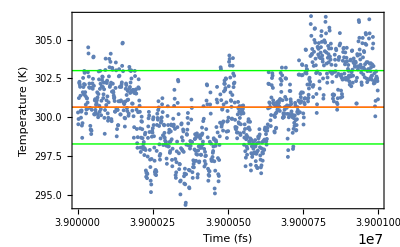

```mathematica
Tprofile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,5]]],2],1;;-1]],Plot[{Tavg,Tavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Temperature (K)"}]
```

```mathematica
Export["graph/Temp_profile.png",Tprofile,ImageResolution->100]
```

graph/Temp_profile.png

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

10.7648

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

444.404

```mathematica
PStdErr=Pstd/(Length[thermo])^0.5
```

14.0533

```mathematica
Pavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

10.7648

```mathematica
Pstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

444.404

```mathematica
PStdErr2=Pstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

14.0533

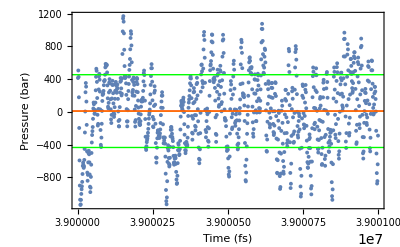

```mathematica
PProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,7]]],2],1;;-1]],Plot[{Pavg,Pavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Pressure (bar)"}]
```

```mathematica
Export["graph/Pressure_profile.png",PProfile,ImageResolution->100]
```

graph/Pressure_profile.png

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

127860.

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

99.426

```mathematica
VolStdErr=Volstd/(Length[thermo])^0.5
```

3.14413

```mathematica
Volavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

127860.

```mathematica
Volstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

99.426

```mathematica
VolStdErr2=Volstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

3.14413

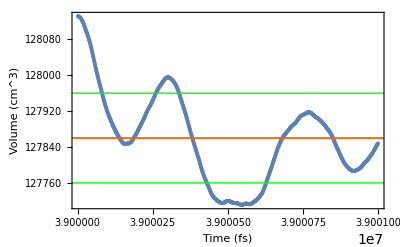

```mathematica
VProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,6]]],2],1;;-1]],Plot[{Volavg,Volavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Volume (cm^3)"}]
```

```mathematica
Export["graph/Volume_profile.png",VProfile,ImageResolution->100]
```

graph/Volume_profile.png

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-8473.15

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

3.41525

```mathematica
EngStdErr=Engstd/(Length[thermo])^0.5
```

0.108

```mathematica
Engavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

-8473.15

```mathematica
Engstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

3.41525

```mathematica
EngStdErr2=Engstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.108

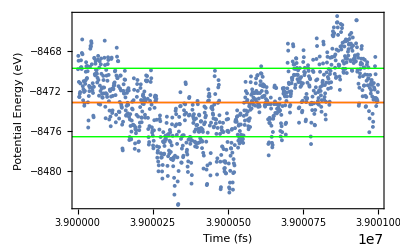

```mathematica
EProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,2]]],2],1;;-1]],Plot[{Engavg,Engavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Potential Energy (eV)"}]
```

```mathematica
Export["graph/Energy_profile.png",EProfile,ImageResolution->100]
```

graph/Energy_profile.png

```mathematica
Lzavg=Mean[thermo[[All,9]]]
```

78.255

```mathematica
Lzstd=StandardDeviation[thermo[[All,9]]]
```

0.0955706

```mathematica
Lzavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

78.255

```mathematica
Lzstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

0.0955706

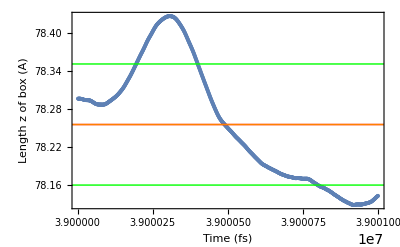

```mathematica
LzProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,9]]],2],1;;-1]],Plot[{Lzavg,Lzavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lzavg2+Lzstd2,Lzavg2-Lzstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length z of box (A)"}]
```

```mathematica
Export["graph/Lz_profile.png",LzProfile,ImageResolution->100]
```

graph/Lz_profile.png

```mathematica
Lxavg=Mean[thermo[[All,8]]]
```

40.4214

```mathematica
Lxstd=StandardDeviation[thermo[[All,8]]]
```

0.0232522

```mathematica
Lxavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

40.4214

```mathematica
Lxstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

0.0232522

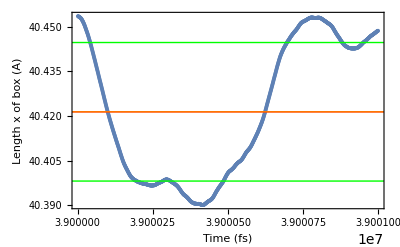

```mathematica
LxProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,8]]],2],1;;-1]],Plot[{Lxavg,Lxavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lxavg2+Lxstd2,Lxavg2-Lxstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length x of box (A)"}]
```

```mathematica
Export["graph/Lx_profile.png",LxProfile,ImageResolution->100]
```

graph/Lx_profile.png